# Running in the Rain

## Predicting Runs based on Environmental Data

Stephen Schroeder

## Introduction

I have been running for several years now, and in September of 2017 I decided that I would start a "run streak." A running streak is defined as running at least 1 mile (1.61 km) every calendar day consecutively. I did this mostly because I found that I couldn't stick to only running 3 or 4 days a week - I would suddenly find myself not having run for several weeks or months! 

Now, almost two years later I have ideas about things that might affect my running, but Wolfram Language allows for so much interesting analysis to be done with my data tracked using RunKeeper! Normally I don’t go out with a plan for how long I will run, and I turn back based on how I am feeling that day. Because of this, one of the main questions that I have about my running data is how my running is affected by temperature. I know that I run less in the Canadian winter, but exactly how much less?

## Running Data Preparation

### Importing Running Data

Previously, I used ServiceConnect to fetch my running data, but unfortunately ServiceConnect does not fetch GPS data from RunKeeper which I will need to be able to get environmental data based on the location, date, and time of my run. 
So, I manually exported my data from my RunKeeper account as explained here, and saved the data to my NotebookDirectory[] with all the GPS files in their own folder. Now, to get started, all the data needs to be imported. I imported the data in a similar fashion to this fantastic Wolfram Blog post, where the running data is parsed using the smart SemanticImport using the column types of the .csv file from RunKeeper.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
runningData = SemanticImport[
	"cardioActivities.csv",
	{"String","Date","String","String",Restricted["Quantity","Kilometers"],
	"String","String",Restricted["Quantity",("Kilometers")/("Hours")],Restricted["Quantity","LargeCalories"],
	Restricted["Quantity","Meters"],"String","String","String","String"
	}
];
```

The GPS Data is slightly more difficult to work with, as each of the 651 runs that I exported have their own .GPX file, and to best deal with the data I only want the coordinates that were recorded at the very beginning of the run.

```mathematica
importGPSData[] := importGPSData[FileNames["*.gpx", "GPS"]]
importGPSData[files_List] := Association@ Map[importGPSData, files]
importGPSData[file_String] :=FileNameTake[file] ->  First @ Cases[
Import[file, "XML"], XMLElement["trkpt",{"lat"->lat_,"lon"->lon_},{_,XMLElement["time",{},{time_}]}] :> {time, lat, lon}, 
Infinity
];

rawGPSData = importGPSData[];
```

Now, so I can best use the GPS data, I will make sure that it is explicitly made up of lists of GeoPositions

```mathematica
GPSData = Map[
GeoPosition@{ToExpression[#[[2]]], ToExpression[#[[3]]]} &, 
rawGPSData
];
```

Lastly, the data needs to be added alongside the rest of the running data imported earlier into our now nice looking dataset!

```mathematica
runningDataWithGPS = Map[
Append[#, "GeoCoord" -> GPSData[#["GPX File"]]]&,
runningData
];
```

### Getting Date-time and Location Specific Temperatures

In order to discover how temperature affects how long I run, I first need to get the data. Thankfully Location and Time-Specific Data is available using the Wolfram Language’s integrated knowledge. I’ll also clean up some missing GPS data to avoid errors.

```mathematica
coords = DeleteCases[Values@Normal@runningDataWithGPS[[All, {"GeoCoord", "Date"}]], {_Missing, _}];
tempData = AirTemperatureData[coords];
```

Finally, all that needs to be done is to add this data to the dataset!

```mathematica
tempDataAssoc = AssociationThread[coords -> tempData];
```

```mathematica
runningDataWithGPSandTemp = Map[
Append[#, "Temperature" -> tempDataAssoc[{#["GeoCoord"],#["Date"]}]]&,
runningDataWithGPS
];
```

```mathematica
DumpSave["fullrundata.mx",{runningDataWithGPSandTemp,coords,tempDataAssoc,tempData}];
```

```mathematica
Get["fullrundata.mx"];
```

## Data Visualisation and Evaluation

Now it' s possible to do tons of analysis of my running data! First, we can see the starting locations of my runs over the past  2 years. Lots of running in icy Canada.

```mathematica
geodata = Flatten[
			Cases[coords,GeoPosition[place__]:>{place},Infinity]
				,1];
```

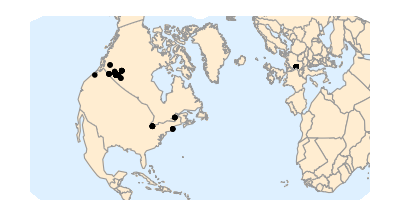

```mathematica
GeoGraphics[GeoMarker[geodata],GeoBackground->"CountryBorders"]
```

The next plot provides real evidence that those cold winters do cause my running distance to go down! It seems like there must be some correlation there.

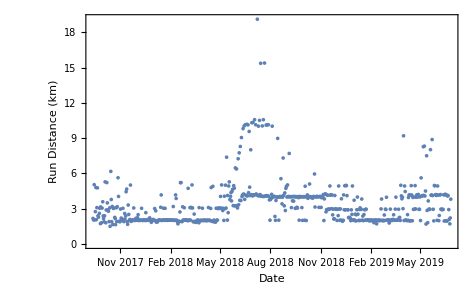

```mathematica
DateListPlot[Query[All,{"Date","Distance (km)"}]@runningDataWithGPSandTemp,Axes->True,FrameLabel->{"Date","Run Distance (km)"},Joined->False,PlotRange->All]
```

The next step is to determine pair the temperature at the time and location of my run with the distance of my run:

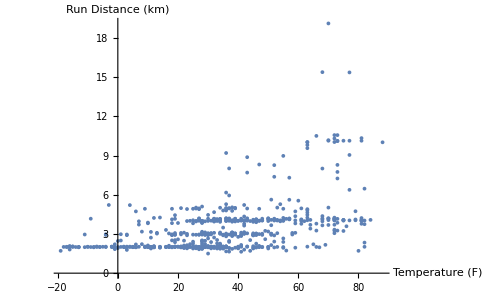

```mathematica
ListPlot[Query[All,{"Temperature","Distance (km)"}]@runningDataWithGPSandTemp,AxesLabel->{"Temperature (F)","Run Distance (km)"},PlotRange->All]
```

Looking at this data, there doesn’t seem to be a great correlation between the temperature and how far I run, but it is still possible to get an idea!

```mathematica
Quantity[1,"Kilometers"]
```

1 km

```mathematica
Values[runningDataWithGPSandTemp//Normal]
```

{{bdb26c9a-8245-4b7c-b207-ff31fe09e98d,Tue 25 Jun 2019 07:34:44GMT-4.,Running,,3.81 km,25:23,6:39,9.01 km/h,285. Cal,85 m,,,,2019-06-25-073444.gpx,GeoPosition[{42.3863,-71.2224}],59 °F},{f45cbd4d-fd22-40c2-9d84-098d06c6eb95,Mon 24 Jun 2019 07:33:12GMT-4.,Running,,2.21 km,12:52,5:50,10.29 km/h,166. Cal,40 m,,,,2019-06-24-073312.gpx,GeoPosition[{42.3865,-71.2223}],65 °F},648,{6fa2612e-5241-4413-8c42-3225203f158f,Tue 12 Sep 2017 07:00:48GMT-4.,Running,,2.17 km,15:00,6:55,8.67 km/h,153. Cal,13 m,,,,2017-09-12-070048.gpx,GeoPosition[{51.0935,-114.16}],69 °F}}
 |  |  |  |

```mathematica
Cases[Values[runningDataWithGPSandTemp//Normal],{Quantity[distance_,"Kilometers"],___,Quantity[temperature_,"DegreesFahrenheit"]}:>{distance->temperature},Infinity]
```

{}

```mathematica
Cases[Values[runningDataWithGPSandTemp//Normal],Quantity[temperature_,"DegreesFahrenheit"]:>temperature,Infinity]
```

{59,65,80,47,46,46,51,55,52,52,55,57,59,57,51,45,45,41,45,50,48,52,67,56,47,50,57,43,50,43,37,46,46,46,43,41,33,37,64,47,52,52,50,45,53,57,31,30,28,27,36,36,37,39,54,39,37,37,50,36,39,32,27,39,30,32,39,39,32,53,36,47,30,36,36,36,30,32,28,34,36,30,34,24,36,36,34,34,36,28,27,36,19,28,41,28,26,21,12,3,-2,3,-6,-15,-18,10,7,-4,-11,-9,0,12,6,5,21,10,-4,1,0,-8,-4,-4,-17,-11,-19,-15,9,-6,-13,-16,-17,-13,2,27,30,16,12,23,48,34,21,5,36,19,19,34,3,1,14,19,19,25,26,46,19,18,18,12,19,23,18,29,45,44,19,7,35,29,18,18,23,18,6,-1,25,28,35,41,32,27,21,45,26,30,30,28,40,23,20,9,1,23,18,25,25,25,23,35,39,47,18,23,22,30,37,34,30,37,36,9,21,48,58,34,19,29,32,14,12,18,16,27,42,29,34,34,38,38,42,38,40,43,42,48,37,33,42,37,39,52,46,44,45,26,28,42,28,24,25,28,32,33,31,28,23,26,27,26,31,34,38,47,40,41,32,29,38,46,38,38,38,36,36,27,28,42,41,51,47,59,55,48,42,43,53,55,70,61,63,59,38,42,49,43,57,62,64,54,60,68,55,64,66,82,79,82,81,81,88,81,73,81,82,82,77,77,81,81,79,73,70,75,68,75,73,72,72,72,81,77,70,66,61,63,72,70,70,72,70,72,72,72,70,81,84,72,68,68,61,63,63,59,73,75,70,68,72,75,66,63,63,63,73,75,77,70,73,72,73,72,73,72,73,77,72,82,75,79,61,66,63,63,68,68,63,61,54,55,55,57,63,52,43,39,55,55,51,41,46,53,46,34,42,34,53,48,42,43,47,39,38,35,40,41,31,27,33,32,36,34,24,27,33,41,24,21,6,6,14,10,11,10,10,5,17,22,29,36,21,23,28,42,22,34,26,23,27,27,22,33,28,26,28,26,22,32,10,13,5,3,6,11,16,20,21,29,19,21,19,4,11,-1,0,-3,4,11,25,3,35,44,11,12,10,-9,2,6,14,8,-8,-5,-2,-2,17,4,-1,2,11,26,25,29,34,29,30,31,39,36,26,17,36,29,-10,-15,-7,17,40,34,45,28,36,30,23,-2,-14,-16,-13,-10,-1,-16,-7,8,17,10,12,12,20,31,30,27,47,26,32,48,33,50,31,36,27,25,33,18,22,29,31,34,34,29,40,33,30,36,47,31,14,37,34,30,7,28,16,36,32,19,31,10,20,9,13,31,37,59,51,28,58,41,51,46,42,51,37,50,50,42,36,30,31,40,38,35,42,52,36,28,33,41,55,76,45,56,49,33,37,38,38,45,35,35,38,43,69}